# Never re-excute commands as files change with time

## Updates

### February 14, 2020

Below are the plots for a version of code that may or may not be version book marked.
Of note is that the convergence of my energy density and pressure’s to Michael Strickland’s is poor, even at early times.
Strickland code: http://personal.kent.edu/~mstrick6/code/index.html - RTA-CUDA v1.0

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Extra

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Project1\output

{-Graphics-}

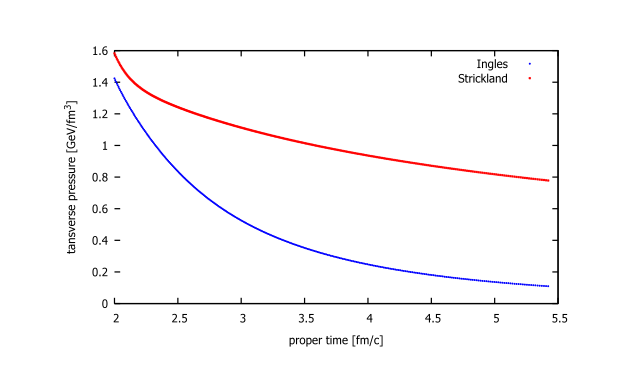

{-Graphics-}

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory["..\\Project1\\output"]
fe=Import["e_evolution.pdf","Pages"]
fpt=Import["pt_evolution.pdf","Pages"]
fpl=Import["pl_evolution.pdf","Pages"]
```

Here is the output from the Gjoko code that I modified, to be colorful. (https://github.com/gvujan/Boltzmann_equation_solver_w_RTA_and_Bjorken_sym)
I may adopt code from Mike McNelis which is more clear and what everything is doing. (https://github.com/mjmcnelis/rta_resum)

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory["Boltzmann_equation_solver_w_RTA_and_Bjorken_sym-master"]
feGojko=Import["e_evolution_gojko.pdf","Pages"]
```

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Extra

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Extra\Boltzmann_equation_solver_w_RTA_and_Bjorken_sym-master

{-Graphics-}

### February 24, 2020

Was able to adjust Gojko’s Mike McNelis’s code to return the energy density in the right units, and plotted this quantity.
As can be seen from the graph, my energy density still has some error at the end.

```mathematica
SetDirectory["C:\\Users\\gil-c\\Documents\\Heinz_Research\\Bjorken_RTA_2\\Project1\\output"]
```

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Project1\output

```mathematica
energDensityLinearScale=Import["e_evolution.pdf", "Pages"]
```

{-Graphics-}

```mathematica
energDensityLogScale = Import["e_evolution.pdf","Pages"]
```

{-Graphics-}

### March 6, 2020

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory["..\\Project1\\output"]
pt10=Import["pTdist_10GeV.dat","Table"];
pt50=Import["pTdist_50GeV.dat","Table"];
```

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Extra

C:\Users\gil-c\Documents\Heinz_Research\Bjorken_RTA_2\Project1\output

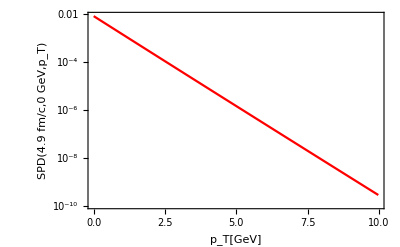

```mathematica
ListLogPlot[pt10,Joined->True,PlotStyle->{2,Red},Frame->True,FrameLabel->{"p_T[GeV]","SPD(4.9 fm/c,0 GeV,p_T)"}]
```

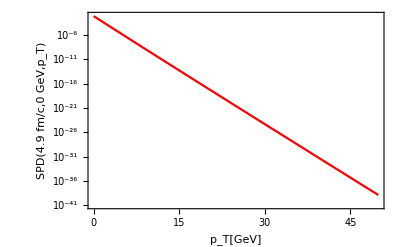

```mathematica
ListLogPlot[pt50,Joined->True,PlotStyle->{2,Red},Frame->True,FrameLabel->{"p_T[GeV]","SPD(4.9 fm/c,0 GeV,p_T)"}]
```

## Scratchwork

```mathematica
data=Import["C:\\Users\\gil-c\\Documents\\Heinz_Research\\Bjorken_RTA_2\\Project1\\output\\T_500.dat","Table"];
```

```mathematica
tau = data[[All, 1]];
Teff = data[[All, 2]];
```

```mathematica
hbarc = 0.197326938;
η = 1/(4π);
tau0 = tau[[1]];
```

```mathematica
LagrangeTemp = Interpolation[data,InterpolationOrder->3];
```

```mathematica
FEQ[ttau_,w_,pT_]:=2/(2π)^3 Exp[-(√(w^2+ pT^2 ttau^2))/(ttau LagrangeTemp[ttau])]
R[z_]:=If[z==0,1,(1/(1+z)+ArcTan[√z]/(√z))1/2];
FINIT[ξ_,w_,pT_]:=2/(2π)^3 Exp[-(√((1+ξ)w^2 + pT^2 tau0^2))/(tau0 LagrangeTemp[tau0])R[ξ]^(1/4)];
```

```mathematica
TEQ[ttau_]:=(5 hbarc η)/LagrangeTemp[ttau];
DECAY[tau1_,tau2_]:=Exp[-NIntegrate[1/TEQ[tt],{tt,tau1,tau2}]]//Quiet;
```

```mathematica
SPD[ttau_,w_,pT_]:=DECAY[tau0,ttau] FINIT[0,w,pT] + NIntegrate[1/TEQ[ttt] DECAY[tau0,ttt] FEQ[ttt,w,pT],{ttt,tau0,ttau},Method->{"Trapezoidal","SymbolicProcessing"->0}]//Quiet;
```

```mathematica
pp=2.0; (*GeV*)
```

```mathematica
feqEvolve=Table[{tau[[ii]],FEQ[tau[[ii]],pp,pp]},{ii,1,Length[tau]}];
teqEvolve=Table[{tau[[ii]],TEQ[tau[[ii]]]},{ii,1,Length[tau]}];
decayEvolve=Table[{tau[[ii]],DECAY[tau[[1]],tau[[ii]]]},{ii,1,Length[tau]}];
(*spdEvolve=Table[{tau[[ii]],SPD[tau[[ii]],2.0,2.0]},{ii,1,Length[tau]}];*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["..\\Project1\\output"];
tevolv=Import["t_evolution.dat","Table"];
t=tevolv[[All,1]];
feq=tevolv[[All,2]];
teq=tevolv[[All,3]];
decay=tevolv[[All,4]];
```

```mathematica
feq=Table[{t[[ii]],feq[[ii]]},{ii,1,Length[t]}];
teq=Table[{t[[ii]],teq[[ii]]},{ii,1,Length[t]}];
decay=Table[{t[[ii]],decay[[ii]]},{ii,1,Length[t]}];
```

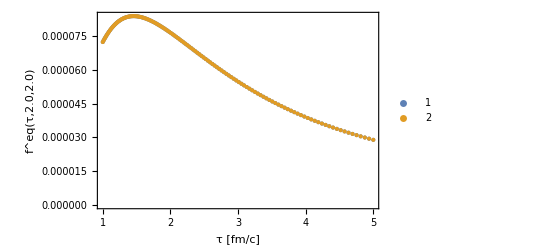

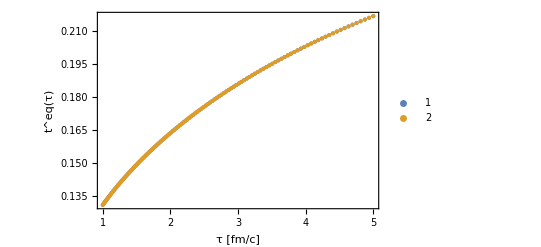

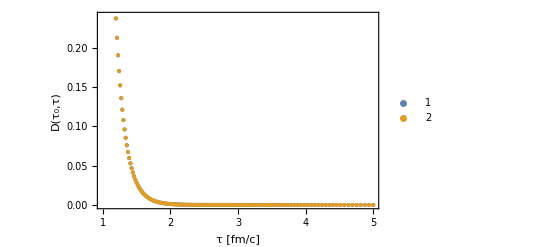

```mathematica
ListPlot[{feqEvolve,feq},Frame->True,FrameLabel->{"τ [fm/c]","f^eq(τ,2.0,2.0)"},PlotLegends->Automatic]
ListPlot[{teqEvolve,teq},Frame->True,FrameLabel->{"τ [fm/c]","t^eq(τ)"},PlotLegends->Automatic]
ListPlot[{decayEvolve,decay},Frame->True,FrameLabel->{"τ [fm/c]","D(τ_0,τ)"},PlotLegends->Automatic]
(*ListPlot[spdEvolve]*)
```

```mathematica
(* Check *)
t0 = 1.0;
t=4.9;
LagrangeTemp[t]
TEQ[t]
DECAY[t0,t]
SPD[t,2.0,2.0]
FEQ[t,2.0,2.0]
FINIT[0,2.0,2.0]
```

0.364275

0.215535

3.07006×10^-10

0.0000774025

0.0000297106

0.0000723114

```mathematica
NIntegrate[FEQ[x,2.0,2.0],{x,0.25,48}]//Quiet
```

0.0000149329

```mathematica
NIntegrate[SPD[x,2.0,2.0],{x,0.25,3}]
```

```mathematica
NIntegrate[1/TEQ[x],{x,0.25,15}]
NIntegrate[DECAY[0.25,x],{x,0.25,15}]
```

41.0607

NIntegrate::nlim: tt = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.150881

```mathematica
ttau = 0.25;
wneg = 4.8381;
wpos = 5.1619;
pTneg = 4.8381;
pTpos = 5.1619;
```

```mathematica
vpospos =√(wpos^2+pTpos^2 ttau^2);
vposneg = √(wpos^2 + pTneg^2 ttau^2);
vnegpos = √(wneg^2+pTpos^2 ttau^2);
vnegneg =√(wneg^2+pTneg^2 ttau^2);
argpospos = pTpos vpospos^2/ttau^2;
argposneg = pTneg vposneg^2/ttau^2;
argnegpos = pTpos vnegpos^2/ttau^2;
argnegneg = pTneg vnegneg^2/ttau^2;
```

```mathematica
Inegneg = argnegneg SPD[ttau,wneg,pTneg]/vnegneg
Inegpos = argnegpos SPD[ttau,wneg,pTpos]/vnegpos
Iposneg = argposneg SPD[ttau,wpos,pTneg]/vposneg
Ipospos = argpospos SPD[ttau,wpos,pTpos]/vpospos
```

1.13314×10^-14

1.0606×10^-14

1.47798×10^-15

1.39381×10^-15

```mathematica
NIntegrate[(4π √(y^2+x^2 tau[[2]]^2)x)/(tau[[2]]^2 hbarc^3)Teff[[2]]^4 SPD[tau[[2]],y Teff[[2]],x Teff[[2]]],{x,0,100},{y,0,100}]//Quiet
```

NIntegrate::nlim: tt = ttt is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.102708 ⅇ^(-NIntegrate[1/TEQ[«1»],{tt,0.25,ttt}]-(√(0.358759 Power[«2»] Power[«2»]+0.358759 Power[«2»]))/(ttt«1»InterpolatingFunction[{{«2»}},{5,7,0,«7»,{},{},False},«1»,{«1»},{Automatic}]«1»«3»])) «1»[ttt] has evaluated to non-numerical values for all sampling points in the region with boundaries {{Indeterminate,Indeterminate}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

10.1877

```mathematica
0.07824421554012398/hbarc^3
```

10.1876

```mathematica
G[τ]=∫∫(4π x √(x^2 τ^2+y^2))/(τ^2 hbarc^3)F[τ,x,y]dx dy
```

```mathematica
NIntegrate[x √(x^2+y^2) Exp[-√(x^2+y^2)], {x,0,1},{y,0,1}]
```

0.174508